# Project report

## SFC Flow

D Malan

Department of Chemistry
University of Pretoria

5 December 2019

## Introduction

The aim of this project is to get a feeling for how much the flow through the SFC is determined by the number of columns.

## Experimental

The SFC pump was filled and set to a pressure of 200 atm. The flow trough the restrictor was measured.
“The choice was a simple linear restrictor and we trusted that heating the end of the restrictor would prevent discrimination. The final linear restrictor was 800mm long and had an internal diameter of 0.050mm.”1
A different number of columns were connected in series, starting with one, and working up to 5. As a control, the flow without any columns connected were also measured.
“The SFC column we used in the SFC×GC system was ... HPLC columns (150mm × 4.6mm, 3μm particles) (Restek, Pinnacle DB Silica) connected in series.”2
The time taken for 50 ml of gaseous carbon dioxide to flow through a bubble flow meter was measured with a hand-held stopwatch, and typed into an Excel spreadsheet.

## Data analysis

Import the data:

```mathematica
data=Import["\\\\chemserv\\CHEMBACK\\HPLC-GC\\Varian-SFC-x-GC#R2-26\\ANAL\\EgmontR\\Niel\\Dropbox\\2019_12_04_SFC_Flow.xlsx", "DataLegacy"];
```

```mathematica
data[[2]][[1;;10]]//Grid
```

Date | Time | Column A |  |  |  |  |  | 
4/12/2019 |  | Fed via  Link 1 |  |  |  |  |  | 
 |  | Volume of gas | Time | Time | Flow |  |  | 
 |  | ml | s | min | ml/min | ml/min | 1. | 
 |  | 50. | 6.29 | 0.104833 | 476.948 |  | 1. | 
 |  | 50. | 6.19 | 0.103167 | 484.653 |  | 1. | 
 |  | 50. | 6.31 | 0.105167 | 475.436 |  | 1. | 
 |  | 50. | 6.15 | 0.1025 | 487.805 |  | 1. | 
 |  | 50. | 6.17 | 0.102833 | 486.224 | 482.213 | 1. | 
 |  |  |  |  |  |  |  |

Data are in the following ranges. The list (a copy & paste from Excel3) gives the line number before the data starts, followed by the number of lines.

```mathematica
datarange=Flatten[#[[1]]+Range[#[[2]]]&/@{{4,5},{13,5},{23,5},{34,6},{45,6},{56,6},{68,6},{79,6},{90,6},{102,6}}]
```

{5,6,7,8,9,14,15,16,17,18,24,25,26,27,28,35,36,37,38,39,40,46,47,48,49,50,51,57,58,59,60,61,62,69,70,71,72,73,74,80,81,82,83,84,85,91,92,93,94,95,96,103,104,105,106,107,108}

```mathematica
Length[datarange]
```

57

```mathematica
flow = data[[2]][[datarange,{6,8}]]
```

{{476.948,1.},{484.653,1.},{475.436,1.},{487.805,1.},{486.224,1.},{480.,2.},{483.871,2.},{483.871,2.},{487.013,2.},{477.707,2.},{473.186,3.},{465.839,3.},{467.29,3.},{468.019,3.},{474.684,3.},{463.679,4.},{461.538,4.},{465.839,4.},{468.75,4.},{475.436,4.},{464.396,4.},{455.235,5.},{465.116,5.},{460.829,5.},{473.934,5.},{472.441,5.},{464.396,5.},{449.775,6.},{459.418,6.},{455.235,6.},{456.621,6.},{457.317,6.},{460.829,6.},{434.153,7.},{436.681,7.},{432.9,7.},{436.681,7.},{436.047,7.},{430.416,7.},{465.116,8.},{470.219,8.},{484.653,8.},{458.015,8.},{470.219,8.},{465.839,8.},{468.75,9.},{460.829,9.},{471.698,9.},{467.29,9.},{469.484,9.},{474.684,9.},{420.757,10.},{424.328,10.},{421.348,10.},{415.512,10.},{421.941,10.},{424.929,10.}}

There are averages in the Excel sheet. The are at the last row of each range.

```mathematica
avgrange = Flatten[#[[1]]+#[[2]]&/@{{4,5},{13,5},{23,5},{34,6},{45,6},{56,6},{68,6},{79,6},{90,6},{102,6}}]
```

{9,18,28,40,51,62,74,85,96,108}

```mathematica
flowavg = data[[2]][[avgrange,{7,8}]]
```

{{482.213,1.},{482.492,2.},{469.803,3.},{466.606,4.},{465.325,5.},{456.533,6.},{434.48,7.},{469.01,8.},{468.789,9.},{421.469,10.}}

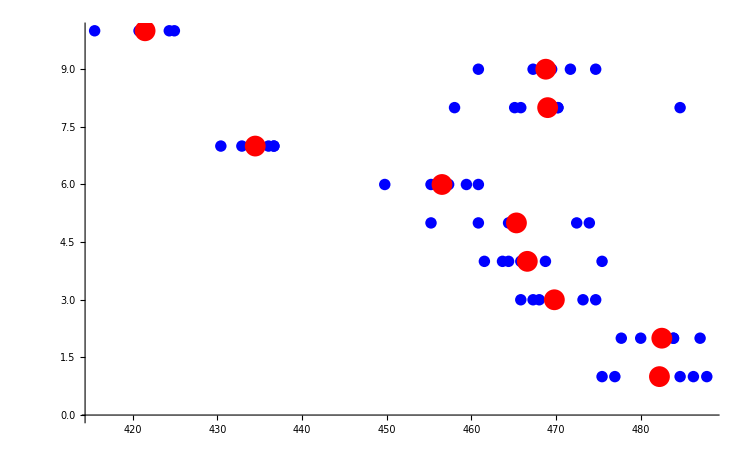

```mathematica
ListPlot[{flow, flowavg},PlotStyle->{Blue, {Red, PointSize[0.02], ChartLabels->{0,0,1,2}}}]
```

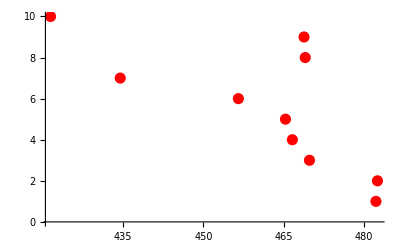

```mathematica
flowavgplot = ListPlot[flowavg, PlotStyle->{Red, PointSize[0.02]}]
```

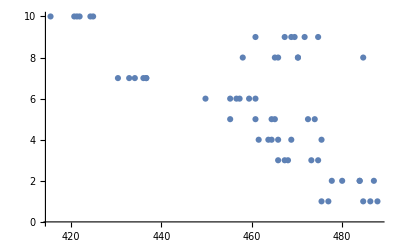

```mathematica
flowplot = ListPlot[flow]
```

Prepare text for annotations:

```mathematica
textlist = {"No. of columns","1","1","2","3", "3", "4", "5", "0", "0", "5"}
```

{No. of columns,1,1,2,3,3,4,5,0,0,5}

```mathematica
textgraphics = MapIndexed[Graphics[Style[Text[#1,{495,#2[[1]]-1}], Medium, Bold]]&, textlist];
```

Combine the graphics:

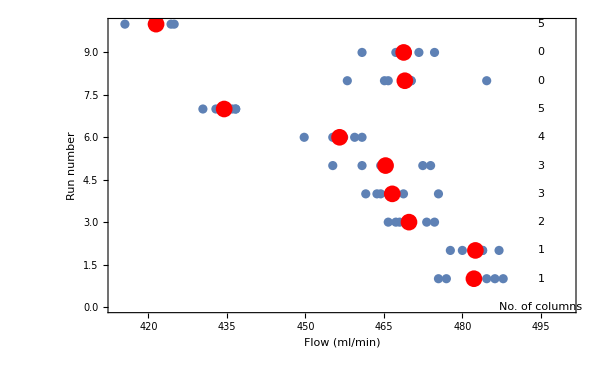

```mathematica
Show[flowplot
, flowavgplot
, textgraphics
,PlotStyle->{Automatic, {Red, PointSize[0.09]}}
,Axes->False
,Frame->{True, True, False, False}
,FrameLabel->{Style["Flow (ml/min)", Large, Black,Bold], Style["Run number", Large, Black, Bold]}
,FrameStyle->Directive[Medium, Bold, Black]
, ImageSize-> 600
,PlotRange ->{ {414,500},Automatic}]
```

## Results

The figure above summarizes the results. It is clear more columns leads to lower flow, but that inter-run repeatability is not very high. For runs 6 and 10 all five columns were in series, but there is a significant difference in flow. For runs 1 and two, with only one column connected, the flow is higher than the flow for runs 8 and 9, where there were no columns. 
None of these observations suggest that the SFC separations will be significantly impacted with 5 columns in series.

## Bibliography

1	Malan, Daniel. 2019. "Fast temperature programmed chromatography coupled to supercritical fluid chromatography (SFC×GC)."

2	Malan, Daniel. 2019. "Fast temperature programmed chromatography coupled to supercritica fluid chromatography (SFC×GC)."

3	https://mathematica.stackexchange.com/questions/8997/cut-and-paste-data-from-a-spreadsheet